#### HW09; Problem 3, Absorption Spectra

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.00364471 | 0.0000424498 | -85.8594 | 3.02537×10^-43
b | 2.98042 | 0.032214 | 92.5192 | 2.0793×10^-44
h | 0.102819 | 0.0016352 | 62.8789 | 2.08469×10^-38
mu | 761.671 | 0.0602916 | 12633.1 | 3.01869×10^-121
sigma | 3.34374 | 0.0661975 | 50.5116 | 5.07578×10^-35

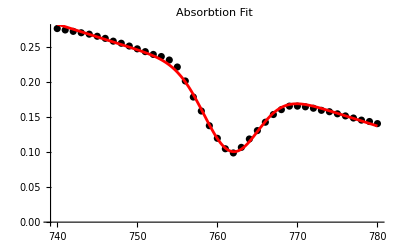

```mathematica
lambda=Range[740,780,1];
i={0.277,0.275,0.273,0.271,0.269,0.266,0.263,0.259,0.256,0.252,0.248,0.244,0.240,0.237,0.232,0.222,0.202,0.179,0.159,0.138,0.120,0.105,0.099,0.107,0.119,0.131,0.143,0.154,0.161,0.166,0.166,0.165,0.163,0.160,0.158,0.155,0.152,0.149,0.146,0.144,0.141};
data=Transpose[{lambda, i}];
(*Define the model:Linear Background-Gaussian Dip*)
model=m*x+b-h*Exp[-(x-mu)^2/(2*sigma^2)];

(*Perform the fit with initial guesses*)
nlm=NonlinearModelFit[data,model,{{m,-0.003},{b,2.5},{h,0.17},{mu,762},{sigma,3}},x];

(*Display the results*)
nlm["ParameterTable"]
Show[ListPlot[data, PlotStyle -> Black,PlotLabel -> "Absorbtion Fit"],
Plot[nlm[x],{x,740,780},  PlotStyle -> Red]]
```